```mathematica
Quit[]
```

### metric

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord];
```

```mathematica
ΩΓ2=1+ξΓ Sum[coord[[i]]^2,{i,n}]
Ω2=1+ξg ΩΓ2^-1 Sum[coord[[i]]^2,{i,n}]
```

1+(h1^2+h2^2+h3^2+h4^2) ξΓ

1+((h1^2+h2^2+h3^2+h4^2) ξg)/(1+(h1^2+h2^2+h3^2+h4^2) ξΓ)

```mathematica
metric=DiagonalMatrix[Table[1/(Ω2 ΩΓ2),{j,n}]]+Table[coord[[i]]coord[[j]],{i,n},{j,n}](6 ξg^2/(Ω2^2 ΩΓ2^4)+6(ξg ξΓ)/(Ω2 ΩΓ2^2)(2-ξΓ/ΩΓ2 Sum[coord[[i]]^2,{i,n}]))//Simplify;
```

{{(h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+(1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h4^2 ξg+h4^2 ξΓ+h2^2 (ξg+ξΓ)+h3^2 (ξg+ξΓ))+h1^2 (ξg+2 (6+h2^2+h3^2+h4^2) ξg ξΓ+6 (h2^2+h3^2+h4^2) ξg ξΓ^2+6 ξg^2 (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h1 h2 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h1 h3 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h1 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2)},{(6 h1 h2 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ+6 h2^2 ξg (ξg+(ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ))/(1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ)^2),(6 h2 h3 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h2 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2)},{(6 h1 h3 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h2 h3 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ+6 h3^2 ξg (ξg+(ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ))/(1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ)^2),(6 h3 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2)},{(6 h1 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h2 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h3 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ+6 h4^2 ξg (ξg+(ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ))/(1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ)^2)}}

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{((1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (6 (h2^2+h3^2+h4^2) ξg^2 ξΓ+2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h4^2 ξΓ+6 h4^2 ξΓ^2+2 h2^2 ξΓ (1+3 ξΓ)+2 h3^2 ξΓ (1+3 ξΓ)))))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))),-((6 h1 h2 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h1 h3 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h1 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))))},{-((6 h1 h2 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),((1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h2^4 ξΓ (ξg+ξΓ)+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (ξg+6 (h3^2+h4^2) ξg^2 ξΓ+2 h3^2 ξg ξΓ (1+3 ξΓ)+2 h4^2 ξg ξΓ (1+3 ξΓ)+2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ))+h1^2 (ξg+2 (6+h2^2+h3^2+h4^2) ξg ξΓ+6 (h2^2+2 (h3^2+h4^2)) ξg ξΓ^2+2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+6 ξg^2 (1+h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))),-((6 h2 h3 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h2 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))))},{-((6 h1 h3 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h2 h3 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),((1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (1+h3^2 ξg+h4^2 ξg+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (ξg+2 (6+h3^2+h4^2) ξg ξΓ+6 (h3^2+2 h4^2) ξg ξΓ^2+2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+6 ξg^2 (1+h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (ξg+2 (6+h2^2+h3^2+h4^2) ξg ξΓ+6 (2 h2^2+h3^2+2 h4^2) ξg ξΓ^2+2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+6 ξg^2 (1+2 h2^2 ξΓ+h3^2 ξΓ+2 h4^2 ξΓ))))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))),-((6 h3 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))))},{-((6 h1 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h2 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h3 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),((1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+6 h3^2 h4^2 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+6 h3^2 h4^2 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (ξg+2 (6+h3^2+h4^2) ξg ξΓ+6 (2 h3^2+h4^2) ξg ξΓ^2+2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+6 ξg^2 (1+2 h3^2 ξΓ+h4^2 ξΓ))+h1^2 (ξg+2 (6+h2^2+h3^2+h4^2) ξg ξΓ+6 (2 h2^2+2 h3^2+h4^2) ξg ξΓ^2+2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+6 ξg^2 (1+2 h2^2 ξΓ+2 h3^2 ξΓ+h4^2 ξΓ))))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))}}

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
riemann:=riemann=ParallelTable[Simplify[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}]],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
ricci:=ricci=ParallelTable[Sum[riemann[[i,j,i,l]],{i,1,n}]//Simplify,{j,1,n},{l,1,n}]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]/.{h1^2->h^2-h2^2-h3^2-h4^2,h1^4->(h^2-h2^2-h3^2-h4^2)^2,h1^6->(h^2-h2^2-h3^2-h4^2)^3,h1^8->(h^2-h2^2-h3^2-h4^2)^4}//FullSimplify
```

(6 (ξg (4+ξg (12+h^2 (1+6 ξg) (5+ξg (6+h^2 (1+6 ξg)))))+(1+6 ξg) (4+h^2 ξg (18+ξg (24+2 h^4 ξg (1+6 ξg)+h^2 (13+42 ξg)))) ξΓ+h^2 (1+6 ξg) (13+ξg (24+h^2 (27+ξg (84+h^4 ξg (1+6 ξg)+h^2 (11+54 ξg))))) ξΓ^2+h^4 (1+6 ξg) (15+ξg (48+3 h^4 ξg (1+6 ξg)+8 h^2 (2+9 ξg))) ξΓ^3+h^6 (1+6 ξg) (7+3 ξg (10+h^2 (1+6 ξg))) ξΓ^4+h^8 (1+6 ξg)^2 ξΓ^5))/(1+h^2 (1+6 ξg) (ξg+h^2 ξg ξΓ+ξΓ (2+h^2 ξΓ)))^2

```mathematica
scalar/.{h->0}//Expand
```

24 ξg+72 ξg^2+24 ξΓ+144 ξg ξΓ

```mathematica
Normal[Series[scalar,{h,∞,0}]]
```

6 (ξg+ξΓ)

```mathematica
Clear[ξΓsol]
```

```mathematica
ξΓsol[ξg_]=ξΓ/.Solve[2 10^-9==1/((1+6ξg)(ξg+ξΓ))(λ NN^2)/(12 π^2),ξΓ][[1]]
```

(125000000 NN^2 λ-3 π^2 ξg-18 π^2 ξg^2)/(3 π^2 (1+6 ξg))

```mathematica
Solve[ξΓsol[ξg]==0/.{NN->60,λ->1},ξg]//N
```

{{ξg→50329.1},{ξg→-50329.3}}

```mathematica
r[ξg_]=(1+6ξg)/(ξg+ξΓsol[ξg])2/NN^2/.{NN->60,λ->1}//Simplify
```

(π+6 π ξg)^2/270000000000000

### inf pheno

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord];
```

```mathematica
ΩΓ2=1+ξΓ Sum[coord[[i]]^2,{i,n}]
Ω2=1+ξg ΩΓ2^-1 Sum[coord[[i]]^2,{i,n}]
```

1+(h1^2+h2^2+h3^2+h4^2) ξΓ

1+((h1^2+h2^2+h3^2+h4^2) ξg)/(1+(h1^2+h2^2+h3^2+h4^2) ξΓ)

```mathematica
metric=DiagonalMatrix[Table[1/(Ω2 ΩΓ2),{j,n}]]+Table[coord[[i]]coord[[j]],{i,n},{j,n}](6 ξg^2/(Ω2^2 ΩΓ2^4)+6(ξg ξΓ)/(Ω2 ΩΓ2^2)(2-ξΓ/ΩΓ2 Sum[coord[[i]]^2,{i,n}]))//Simplify;
```

```mathematica
metric/.{h1->x,h2->0,h3->0,h4->0}//Simplify
```

{{(1+x^4 (1+6 ξg) ξΓ (ξg+ξΓ)+x^2 (1+6 ξg) (ξg+2 ξΓ))/((1+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^2),0,0,0},{0,1/(1+x^2 (ξg+ξΓ)),0,0},{0,0,1/(1+x^2 (ξg+ξΓ)),0},{0,0,0,1/(1+x^2 (ξg+ξΓ))}}

```mathematica
KK[x_]=Simplify[Eigenvalues[metric][[4]]]/.{h1^2->x^2-h2^2-h3^2-h4^2,h1^4->(x^2-h2^2-h3^2-h4^2)^2}//Simplify
```

(1+x^4 (1+6 ξg) ξΓ (ξg+ξΓ)+x^2 (1+6 ξg) (ξg+2 ξΓ))/((1+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^2)

```mathematica
Eigenvalues[metric/.{h1->x/2,h2->x/2,h3->x/2,h4->x/2}//Simplify]//Simplify
```

{1/(1+x^2 (ξg+ξΓ)),1/(1+x^2 (ξg+ξΓ)),1/(1+x^2 (ξg+ξΓ)),(1+x^4 (1+6 ξg) ξΓ (ξg+ξΓ)+x^2 (1+6 ξg) (ξg+2 ξΓ))/((1+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^2)}

```mathematica
Normal[Series[Sqrt[KK[x]],{x,0,2}]]
```

1+1/2 x^2 (-ξg+6 ξg^2-ξΓ+12 ξg ξΓ)

```mathematica
VV[x_]=x^4/(4 ΩΓ2^2 Ω2^2)/.{h1->x,h2->0,h3->0,h4->0}//Simplify;
```

```mathematica
HH[x_,p_]=Sqrt[(KK[x]/2 p^2+VV[x])/3];
ϵH[x_,p_]=(KK[x] p^2)/(2 HH[x,p]^2);
```

```mathematica
c3=ξg ξΓ^2+ξΓ^3+6 ξg^2 ξΓ^2+6ξg ξΓ^3;
c7=ξΓ^2(ξg+ξΓ)^2;
```

```mathematica
AA=Sqrt[c7/c3]//Simplify
```

√((ξg+ξΓ)/(1+6 ξg))

```mathematica
Normal[Series[VV[x],{x,∞,2}]]
```

-1/(2 x^2 (ξg+ξΓ)^3)+1/(4 (ξg+ξΓ)^2)

```mathematica
ξgs=10^4;
ξΓs=10^6;
xin=Sqrt[(8 AA^2)/(ξg+ξΓ)NN]/.{ξg->ξgs,ξΓ->ξΓs,NN->80};
Hin=HH[xin,0]/.{ξg->ξgs,ξΓ->ξΓs};
tf=100/Hin;
```

```mathematica
Sqrt[(8 AA^2)/(ξg+ξΓ)]/.{ξg->ξgs,ξΓ->ξΓs}//N
```

0.0115469

```mathematica
sol=NDSolve[{x''[t]+(3HH[x[t],x'[t]]+KK'[x[t]]/(2KK[x[t]])x'[t])x'[t]+VV'[x[t]]/KK[x[t]]==0,x[0]==xin,x'[0]==0,NN'[t]==HH[x[t],x'[t]],NN[0]==0}/.{ξg->ξgs,ξΓ->ξΓs},{x[t],x'[t],NN[t]},{t,0,tf}][[1]]
```

{x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],NN[t]→InterpolatingFunction[…][t]}

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=HH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵsol[t_]=(KK[xsol[t]] psol[t]^2)/(2 Hsol[t]^2)/.{ξg->ξgs,ξΓ->ξΓs};
```

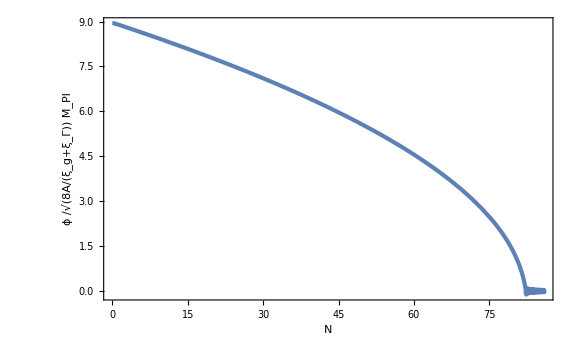

```mathematica
ParametricPlot[{Nsol[t],xsol[t]/Sqrt[(8 AA^2)/(ξg+ξΓ)]/.{ξg->ξgs,ξΓ->ξΓs}},{t,0,tf},PlotRange->Full,FrameLabel->{N,Row[{ϕ," /",Sqrt["8A/(ξ_g+ξ_Γ)"] Subscript[M, Pl]}]}]
```

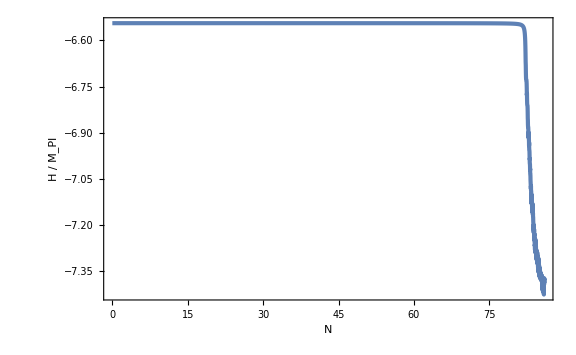

```mathematica
ParametricPlot[{Nsol[t],Log10[Hsol[t]]},{t,0,tf},PlotRange->Full,FrameLabel->{N,Row[{H," / ",Subscript[M, Pl]}]}]
```

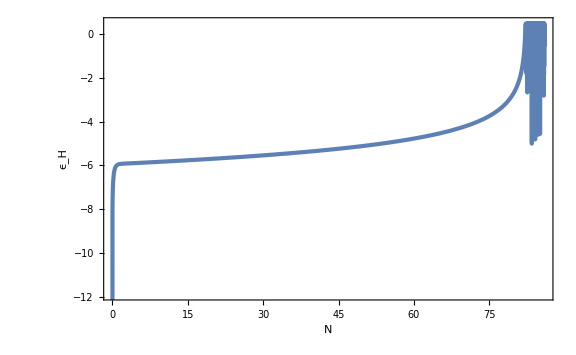

```mathematica
ParametricPlot[{Nsol[t],Log10[ϵsol[t]]},{t,0,tf},FrameLabel->{N,Subscript[ϵ, H]}]
```

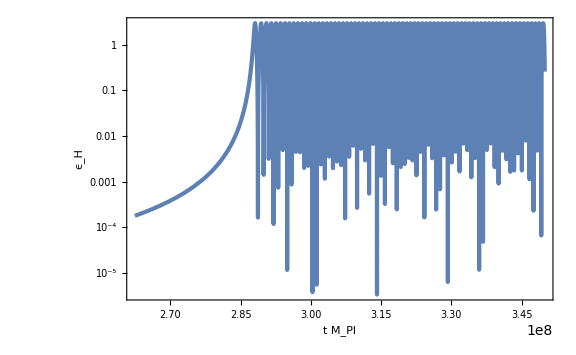

```mathematica
LogPlot[ϵsol[t],{t,3/4 tf,tf},GridLines->{{4/5 tf},None},FrameLabel->{Subscript[M, Pl] t,Subscript[ϵ, H]}]
```

```mathematica
Fakeϵ[t_]=eH[t]/.NDSolve[{eH'[t]==Abs[ϵsol'[t]],eH[0]==0},eH[t],{t,0,tf}][[1]]
```

8
InterpolatingFunction[{{0., 3.49907 10 }}, <>][t]

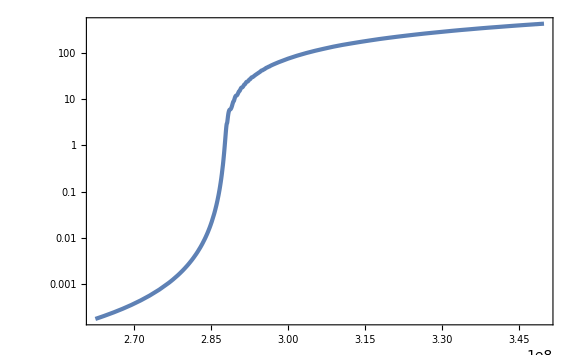

```mathematica
LogPlot[Fakeϵ[t],{t,3/4 tf,tf},GridLines->{{4/5 tf},{1}}]
```

```mathematica
tend=t/.FindRoot[Log[Fakeϵ[t]]==0,{t,4/5 tf}]
Nend=Nsol[tend]
Ns=Nend-55
ts=t/.FindRoot[Nsol[t]==Ns,{t,1/4 tf}]
```

2.87657×10^8

82.1471

27.1471

9.49915×10^7

```mathematica
tensor=16ϵsol[ts]
ranal=(1+6ξg)/(ξg+ξΓ)2/NN^2/.{ξg->ξgs,ξΓ->ξΓs,NN->55}//N
```

0.0000412773

0.0000392773

```mathematica
calP=1/(24 π^2)VV[xsol[ts]]/ϵsol[ts]/.{ξg->ξgs,ξΓ->ξΓs}
calPanal=1/((1+6ξg)(ξg+ξΓ))NN^2/(12 π^2)/.{ξg->ξgs,ξΓ->ξΓs,NN->55}//N
```

4.00935×10^-10

4.21468×10^-10